```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"out","poiseuilleMB"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/poiseuilleMB

```mathematica
srtVels = Complement[FileNames["*velocity"], FileNames["*time"], FileNames["cumulant*"]];
cumulantVels = Complement[FileNames["*velocity"], FileNames["*time"], FileNames["srt*"]];
srtPressures = Complement[FileNames["*density"], FileNames["*time"], FileNames["cumulant*"]];
cumulantPressures = Complement[FileNames["*density"], FileNames["*time"], FileNames["srt*"]];
getLengths[thelist_]:=Read[StringToStream[#],Number]&/@Flatten[ StringDrop[#,6] &/@StringCases[thelist, RegularExpression["length([0-9]*)"]]] ;
lengths = getLengths[srtVels];
permutations = Ordering[lengths];
srtVels = srtVels[[permutations]];
cumulantVels = cumulantVels[[permutations]];
srtPressures = srtPressures[[permutations]];
cumulantPressures = cumulantPressures[[permutations]];
lengths = lengths[[permutations]];

myPlot[val_,labels_, drop_]:=ListLinePlot[Drop[val,drop], PlotLegends->Drop[labels,drop], PlotRange->All];
myPlotFromTo[val_,labels_, from_, to_]:=ListLinePlot[Part[val,from;;to], PlotLegends->Part[labels,from;;to], PlotRange->All];
```

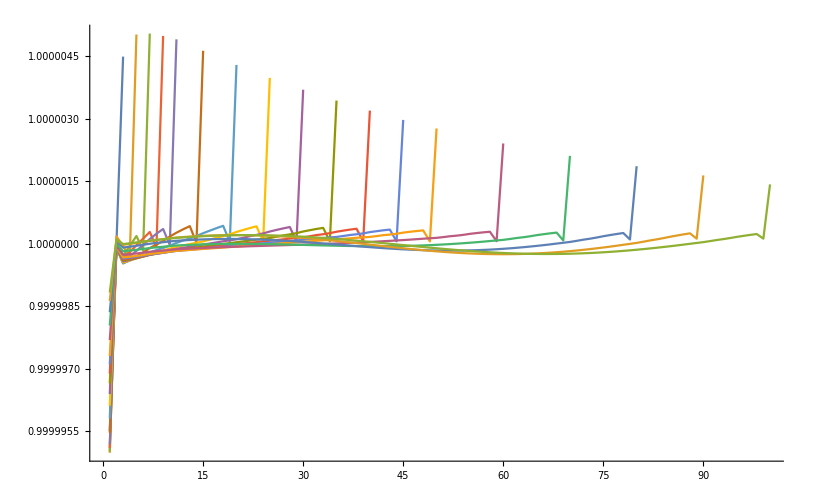

```mathematica
values =  Import[#,"List"]& /@ cumulantPressures;
ListLinePlot[values, PlotRange->All]
```